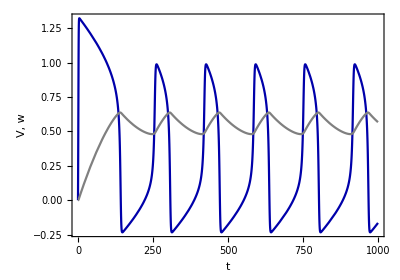

```mathematica
eqV[V_,w_]:=A*V(1-V)*(V-Vs)-w  + Iext
eqw[V_,w_]:=ϵ(V-c*w)
pars = {A->1, Vs->0.2, c-> 0.4, ϵ->0.005, Iext-> 0.5};
sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tEnd = 1000.0;
init = Thread[{V[0], w[0]} == {0.0, 0.0} ];
solution = NDSolve[Join[sys, init], vars, {t, 0, tEnd}];
Plot[Evaluate[vars /. solution], {t, 0, tEnd}, PlotRange -> All, PlotStyle ->{Darker[Blue],Gray},Frame -> True,  FrameLabel -> {"t", "V, w"}, AspectRatio -> 0.7]
```

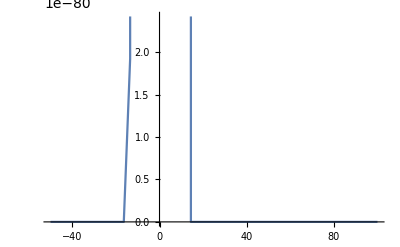

```mathematica
pars = {A->1, Vs->0.2, c-> 0.4, ϵ->0.005, σ->1.0, I0->0.1422, T->600};
Iext[t_]:=I0*Sum[Exp[-(t - j*T)^2/σ^2], {j, -Infinity, Infinity}]
Plot[Iext[t]/.pars, {t, -50, 100}]
```

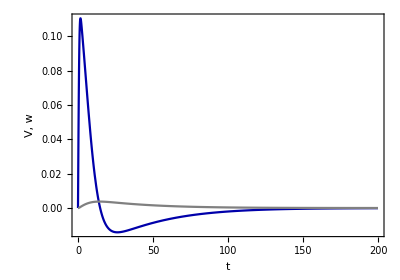

```mathematica
Iext[t_]:=I0*Sum[Exp[-(t - j*T)^2/σ^2], {j, -Infinity, Infinity}]
eqV[V_,w_]:=A*V(1-V)*(V-Vs)-w  +Iext[t]
eqw[V_,w_]:=ϵ(V-c*w)
pars = {A->1, Vs->0.2, c-> 0.4, ϵ->0.005, σ->1.0, I0->0.1422, T->600};
sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tEnd = 200;
init = Thread[{V[0], w[0]} == {0.0, 0.0} ];
solution = NDSolve[Join[sys, init], vars, {t, 0, tEnd}];
Plot[Evaluate[vars /. solution], {t, 0, tEnd}, PlotRange -> All, PlotStyle ->{Darker[Blue],Gray},Frame -> True,  FrameLabel -> {"t", "V, w"}, AspectRatio -> 0.7]
```

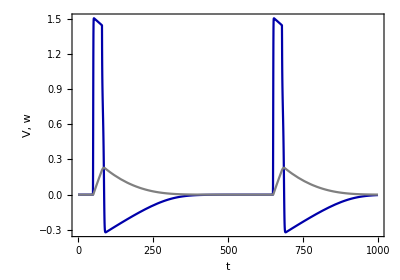

```mathematica
stimuliTrain[t_, A_,duty_, period_]:=A*UnitBox[Mod[t/period,1.]/(2. duty)]
eqV[V_,w_]:=A*V(1-V)*(V-Vs)-w  +stimuliTrain[t-d, A,duration,T]
eqw[V_,w_]:=ϵ(V-c*w)
pars = {A->1, Vs->0.2, c-> 0.4, ϵ->0.005, σ->1.0, d->50, A->0.5, duration->0.05,T->600};
sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tEnd = 1000;
init = Thread[{V[0], w[0]} == {0.0, 0.0} ];
solution = NDSolve[Join[sys, init], vars, {t, 0, tEnd}];
Plot[Evaluate[vars /. solution], {t, 0, tEnd}, PlotRange -> All, PlotStyle ->{Darker[Blue],Gray},Frame -> True,  FrameLabel -> {"t", "V, w"}, AspectRatio -> 0.7]
```

{{V→-1.19941,w→-0.62426}}

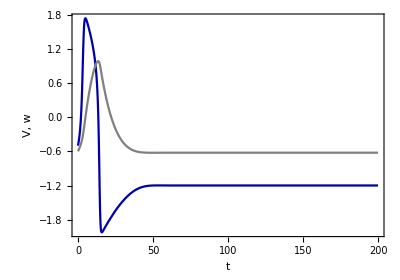

```mathematica
eqV[V_,w_]:=V-V^3/3-w+ S
eqw[V_,w_]:=1/τ(V+a-b w)
pars={a->0.7,b->0.8,τ->12.5, S->0.0};
eql = NSolve[{eqV[V, w] == 0.0, eqw[V, w] == 0.0} /. pars, {V, w}, Reals]
sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tEnd = 200.0;
init = Thread[{V[0], w[0]} == {-0.5,-0.6} ];
solution = NDSolve[Join[sys, init], vars, {t, 0, tEnd}];
Plot[Evaluate[vars /. solution], {t, 0, tEnd}, PlotRange -> All, PlotStyle ->{Darker[Blue],Gray},Frame -> True,  FrameLabel -> {"t", "V, w"}, AspectRatio -> 0.7]
```

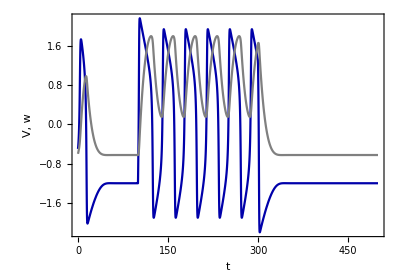

```mathematica
eqV[V_,w_]:=V-V^3/3-w+ S[t]
eqw[V_,w_]:=1/τ(V+a-b w)
pars={a->0.7,b->0.8,τ->12.5, Subscript[T, on]->100,Subscript[T, off]->300,Subscript[i, on]->1.0};

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
stimulus={WhenEvent[t==Subscript[T, on],S[t]->Subscript[i, on]],WhenEvent[t==Subscript[T, off],S[t]->0.0]}/.pars;
vars = {V[t], w[t]};
tEnd = 500.0;
init = Thread[{V[0], w[0], S[0]} == {-0.5,-0.6, 0.0} ];
solution = NDSolve[Join[sys, init, stimulus], vars, {t, 0, tEnd}, DiscreteVariables->S];
Plot[Evaluate[vars /. solution], {t, 0, tEnd}, PlotRange -> All, PlotStyle ->{Darker[Blue],Gray},Frame -> True,  FrameLabel -> {"t", "V, w"}, AspectRatio -> 0.7]
```

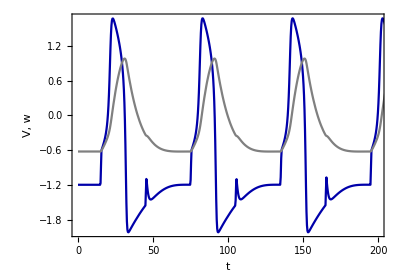

```mathematica
stimuliTrain[t_, A_,duty_, period_]:=A*UnitBox[Mod[t/period,1.]/(2. duty)]
eqV[V_,w_]:=V-V^3/3-w+ stimuliTrain[t-d, A,duration,T]
eqw[V_,w_]:=1/τ(V+a-b w)
pars={a->0.7,b->0.8,τ->12.5, d->15,A->1, duration->0.02, T->30};

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tEnd = 1000.0;
init = Thread[{V[0], w[0]} == {-1.19941,-0.62426} ];
solution = NDSolve[Join[sys, init], vars, {t, 0, tEnd}];
Plot[Evaluate[vars /. solution], {t, 0, tEnd}, PlotRange -> {{0, 200}, All}, PlotStyle ->{Darker[Blue],Gray},Frame -> True, FrameLabel -> {"t", "V, w"}, AspectRatio -> 0.7]
```